{4.69984,4.69518,4.70994,4.70235,4.70257,4.69184,4.6969,4.69402,4.69031,4.69117,4.69825,4.7101,4.68595,4.67256,4.69551,4.69989,4.69827,4.70182,4.70134,4.68263,4.70677,4.69864,4.70164,4.70223,4.70327,4.69254,4.69294,4.69649,4.69215,4.69124,4.70526,4.6972,4.69848,4.68801,4.69246,4.69397,4.68952,4.6814,4.69903,4.68721,4.69683,4.713,4.68436,4.69188,4.70563,4.70935,4.68061,4.7179,4.701,4.69234,4.69937,4.68337,4.7053,4.69688,4.72119,4.67699,4.69488,4.68673,4.69361,4.72146,4.70347,4.70534,4.70214,4.68776,4.69741,4.69188,4.69458,4.69398,4.70219,4.68319,4.70169,4.71353,4.69065,4.68729,4.68328,4.70838,4.68511,4.69697,4.69977,4.6875,4.72119,4.68973,4.69057,4.69582,4.68036,4.71657,4.67325,4.70743,4.69607,4.69464,4.68697,4.69183,4.71169,4.69284,4.71057,4.68486,4.68446,4.72287,4.69007,4.69946,4.68604,4.69186,4.69086,4.68274,4.70265,4.69288,4.69564,4.70157,4.68558,4.71496,4.69426,4.6993,4.68191,4.70775,4.67869,4.69335,4.69404,4.68519,4.70328,4.70078,4.70298,4.6865,4.69732,4.70234,4.69557,4.68458,4.68684,4.69108,4.69088,4.68667,4.69031,4.70091,4.69181,4.68456,4.68866,4.69707,4.68966,4.69191,4.7015,4.69919,4.68459,4.69098,4.69376,4.7064,4.69925,4.69371,4.67373,4.71772,4.69022,4.69823,4.69507,4.66808,4.69596,4.70323,4.67885,4.69459,4.68371,4.6958,4.68992,4.71553,4.68537,4.69661,4.68802,4.68144,4.70387,4.69564,4.70599,4.69258,4.69148,4.68246,4.68686,4.68965,4.69569,4.7092,4.6956,4.68203,4.70334,4.69194,4.70481,4.71096,4.69525,4.69481,4.69198,4.69304,4.69086,4.68551,4.689,4.6791,4.68353,4.69257,4.68033,4.69717,4.69452,4.68074,4.68755,4.71345,4.69503,4.67895,4.68338,4.68381}

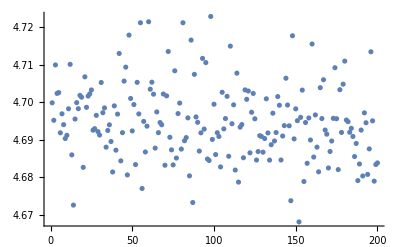

```mathematica
coule=Table[codbar[[j]][[3]],{j,200}]
ListPlot[coule]
```

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/CFL_coule_dbar/CFL_coule_vsdbar","Table"];
NN=Length[codbar];
n=420
d=Table[codbar[[i]][[1]],codbar[[i]][[2]],{i,1,n}]
Table[codbar[[n*(i-1)+j]][[3]],{i,1,1},{j,1,5}];
ListPointPlot3D[%]
```

420

Part::pkspec1: The expression i cannot be used as a part specification.

Table::iterb: Iterator {i} does not have appropriate bounds.

Table[codbar⟦i⟧⟦1⟧,{i},{i,1,n}]

-Graphics3D-

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/coulenergy_jie","Table"];
codbar
Table[codbar[[90*(i-1)+j]][[3]],{i,1,90,1},{j,1,90,1}];
ListPointPlot3D[%]
```

{{0,0,-0.39278},{0,1,-0.443663},{0,2,-0.40382},{0,3,-0.44126},{0,4,-0.411569},{0,5,-0.425231},{0,6,-0.424979},{0,7,-0.428307},{0,8,-0.420035},{0,9,-0.410465},{0,10,-0.439407},8078,{89,79,-0.427526},{89,80,-0.409018},{89,81,-0.436984},{89,82,-0.423447},{89,83,-0.45245},{89,84,-0.428586},{89,85,-0.438226},{89,86,-0.425911},{89,87,-0.445082},{89,88,-0.433644},{89,89,-0.422183}}
 |  |  |  |

-Graphics3D-